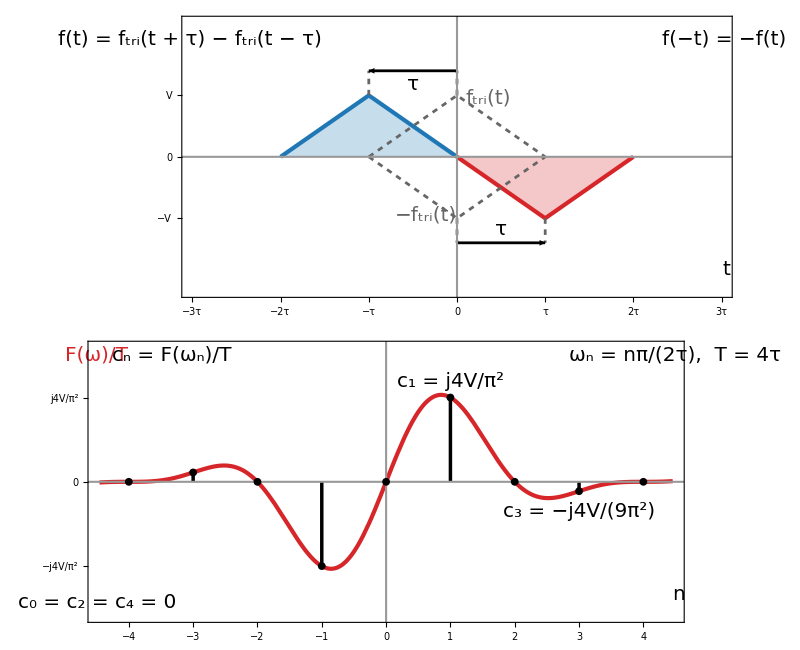

```mathematica
ClearAll[fs,vv,tau,blue,red,gray,env,cn,wn,label,tL,nL,ticksT,ticksN,tyT,tyF,stems,pts,g1,g2,fig];

fs=20;      (*tamaño de fuente único*)
vv=1;       (*amplitud V*)
tau=1;      (*τ*)

blue=RGBColor[0.12,0.47,0.71];
red=RGBColor[0.84,0.15,0.16];
gray=GrayLevel[0.4];

(*F(ω)/T en unidades de jV,con x=ωτ y T=4τ*)
env[x_]:=1/2 Sin[x] Sinc[x/2]^2;
(*c_n en unidades de jV*)
cn[n_]:=1/2 Sin[n Pi/2] Sinc[n Pi/4]^2;
(*ω_n=nπ/(2τ)*)
wn[n_]:=N[n Pi/(2 tau)];

(*Texto con tamaño fs;pos puede ser una lista o Scaled[...]*)
label[expr_,col_,pos_,off_List:{-1,0}]:=Text[Style[expr,fs,col],pos,off];

tL={"−3τ","−2τ","−τ","0","τ","2τ","3τ"};
ticksT=Table[{(k-4) tau,Style[tL[[k]],fs]},{k,7}];
tyT={{-vv,Style["−V",fs]},{0,Style["0",fs]},{vv,Style["V",fs]}};

nL={"−4","−3","−2","−1","0","1","2","3","4"};
ticksN=Table[{wn[k-5],Style[nL[[k]],fs]},{k,9}];
tyF={{N[-4/Pi^2],Style[Row[{"−j4V/",Superscript["π",2]}],fs]},{0,Style["0",fs]},{N[4/Pi^2],Style[Row[{"j4V/",Superscript["π",2]}],fs]}};

(*Panel 1:f(t)=f_tri(t+τ)−f_tri(t−τ)*)
g1=Graphics[{{Opacity[0.25,blue],EdgeForm[None],Polygon[{{-2 tau,0},{-tau,vv},{0,0}}]},{Opacity[0.25,red],EdgeForm[None],Polygon[{{0,0},{tau,-vv},{2 tau,0}}]},{blue,AbsoluteThickness[3],Line[{{-2 tau,0},{-tau,vv},{0,0}}]},{red,AbsoluteThickness[3],Line[{{0,0},{tau,-vv},{2 tau,0}}]}},PlotRange->{{-3 tau,3 tau},{-2.2,2.2}},PlotRangePadding->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicks->{{tyT,None},{ticksT,None}},GridLines->{{0},{0}},GridLinesStyle->Directive[GrayLevel[0.6],AbsoluteThickness[1.5]],Background->White,AspectRatio->0.4,ImagePadding->{{110,15},{45,10}},Epilog->{(*pulsos de referencia sin desplazar*){gray,AbsoluteThickness[2],Dashing[{0.01,0.01}],Line[{{-tau,0},{0,vv},{tau,0}}],Line[{{-tau,0},{0,-vv},{tau,0}}],Line[{{0,vv},{0,1.4 vv}}],Line[{{-tau,vv},{-tau,1.4 vv}}],Line[{{0,-vv},{0,-1.4 vv}}],Line[{{tau,-vv},{tau,-1.4 vv}}]},(*flechas de desplazamiento*){Black,AbsoluteThickness[2],Arrowheads[0.02],Arrow[{{0,1.4 vv},{-tau,1.4 vv}}],Arrow[{{0,-1.4 vv},{tau,-1.4 vv}}]},label["τ",Black,{-tau/2,1.18 vv},{0,0}],label["τ",Black,{tau/2,-1.18 vv},{0,0}],label[Row[{Subscript["f","tri"],"(t)"}],gray,{0.35 tau,0.95 vv}],label[Row[{"−",Subscript["f","tri"],"(t)"}],gray,{-0.35 tau,-0.95 vv},{1,0}],label[Row[{"f(t) = ",Style[Row[{Subscript["f","tri"],"(t + τ)"}],blue]," − ",Style[Row[{Subscript["f","tri"],"(t − τ)"}],red]}],Black,Scaled[{0.015,0.92}]],label["f(−t) = −f(t)",Black,Scaled[{0.985,0.92}],{1,0}],label["t",Black,Scaled[{0.99,0.1}],{1,0}]}];

(*Panel 2:espectro F(ω)/T muestreado en ω_n=nπ/(2τ)*)
stems=Table[Line[{{wn[n],0},{wn[n],N[cn[n]]}}],{n,-4,4}];
pts=Point[Table[{wn[n],N[cn[n]]},{n,-4,4}]];

g2=Plot[env[w tau],{w,-7/tau,7/tau},PlotRange->{{-7/tau,7/tau},{-0.65,0.65}},PlotRangePadding->None,PlotStyle->Directive[red,AbsoluteThickness[3]],Background->White,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicks->{{tyF,None},{ticksN,None}},GridLines->{{0},{0}},GridLinesStyle->Directive[GrayLevel[0.6],AbsoluteThickness[1.5]],AspectRatio->0.4,ImagePadding->{{110,15},{45,10}},Epilog->{{Black,AbsoluteThickness[2.5],stems},{Black,PointSize[0.014],pts},label["F(ω)/T",red,Scaled[{0.015,0.95}]],label[Row[{Subscript["c","n"]," = F(",Subscript["ω","n"],")/T"}],Black,Scaled[{0.14,0.95}]],label[Row[{Subscript["ω","n"]," = nπ/(2τ),  T = 4τ"}],Black,Scaled[{0.985,0.95}],{1,0}],label[Row[{Subscript["c",1]," = j4V/",Superscript["π",2]}],Black,{wn[1],N[cn[1]]+0.075},{0,0}],label[Row[{Subscript["c",3]," = −j4V/(9",Superscript["π",2],")"}],Black,{wn[3],N[cn[3]]-0.1},{0,0}],label[Row[{Subscript["c",0]," = ",Subscript["c",2]," = ",Subscript["c",4]," = 0"}],Black,Scaled[{0.015,0.07}]],label["n",Black,Scaled[{0.99,0.1}],{1,0}]}];

fig=GraphicsColumn[{g1,g2},Spacings->0,Background->White,ImageSize->800]
```

```mathematica
Export["T2_Transformada_P2.png",fig,ImageResolution->300]
```

T2_Transformada_P2.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["T2_Transformada_P2.png"]]]
```